```mathematica
ϕ=.
H={{Subscript[ϵ, k],Δ,ϕ,0 },{Δ,-Subscript[ϵ, k],0,-ϕ},{ϕ,0,Subscript[ϵ, k],0},{0,-ϕ,0,-Subscript[ϵ, k]}};
MatrixForm[H]
Assuming[{{Subscript[ϵ, k],Δ},Real},{{evals,evecs}=Eigensystem[H]}];
evals
Subscript[n, 1]=Norm[FullSimplify[evecs[[1]]]];
Subscript[n, 2]=Norm[FullSimplify[evecs[[2]]]];
Subscript[n, 3]=Norm[FullSimplify[evecs[[3]]]];
Subscript[n, 4]=Norm[FullSimplify[evecs[[4]]]];
DN=DiagonalMatrix[{Subscript[n, 1],Subscript[n, 2],Subscript[n, 3],Subscript[n, 4]}];
DN//MatrixForm
Ut=FullSimplify[Transpose[evecs]];
MatrixForm[Ut]
MatrixForm[FullSimplify[Transpose[Ut].H.Ut]]
MatrixForm[FullSimplify[Transpose[Ut].Ut]];
MatrixForm[FullSimplify[Inverse[Ut].Ut]];
```

(ϵ_k | Δ | ϕ | 0
Δ | -ϵ_k | 0 | -ϕ
ϕ | 0 | ϵ_k | 0
0 | -ϕ | 0 | -ϵ_k)

{-(√(Δ^2+2 ϕ^2+2 ϵ_k^2-√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2),(√(Δ^2+2 ϕ^2+2 ϵ_k^2-√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2),-(√(Δ^2+2 ϕ^2+2 ϵ_k^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2),(√(Δ^2+2 ϕ^2+2 ϵ_k^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2)}

(√(1+Abs[(-ϵ_k+√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/ϕ]^2+Abs[(ϕ^3-ϕ (ϵ_k-√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ^2)]^2+Abs[(ϕ^3-ϕ (ϵ_k-√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ (ϵ_k+√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))))]^2) | 0 | 0 | 0
0 | √(1+Abs[(ϵ_k+√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/ϕ]^2+Abs[(ϕ^3-1/4 ϕ (2 ϵ_k+√(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ^2)]^2+Abs[(ϕ^3-1/4 ϕ (2 ϵ_k+√(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ (ϵ_k-√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))))]^2) | 0 | 0
0 | 0 | √(1+Abs[(-ϵ_k+(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2))/ϕ]^2+Abs[(ϕ^3-ϕ (ϵ_k-(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2))^2)/(Δ ϕ^2)]^2+Abs[(ϕ^3-ϕ (ϵ_k-(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2))^2)/(Δ ϕ (ϵ_k+(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2)))]^2) | 0
0 | 0 | 0 | √(1+Abs[(ϵ_k+(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2))/ϕ]^2+Abs[(ϕ^3-1/4 ϕ (2 ϵ_k+√2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ^2)]^2+Abs[(ϕ^3-1/4 ϕ (2 ϵ_k+√2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ (ϵ_k-(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2)))]^2))

((ϕ^3-ϕ (ϵ_k-√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ^2) | (ϕ^3-1/4 ϕ (2 ϵ_k+√(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ^2) | (ϕ^3-ϕ (ϵ_k-(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2))^2)/(Δ ϕ^2) | (ϕ^3-1/4 ϕ (2 ϵ_k+√2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ^2)
(-ϵ_k+√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/ϕ | -(ϵ_k+√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/ϕ | (-ϵ_k+(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2))/ϕ | -(ϵ_k+(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2))/ϕ
-(ϕ^3-ϕ (ϵ_k-√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ (ϵ_k+√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))) | -(ϕ^3-1/4 ϕ (2 ϵ_k+√(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ (ϵ_k-√(Δ^2/2+ϕ^2+ϵ_k^2-1/2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))) | -(ϕ^3-ϕ (ϵ_k-(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2))^2)/(Δ ϕ (ϵ_k+(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2))) | -(ϕ^3-1/4 ϕ (2 ϵ_k+√2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2)/(Δ ϕ (ϵ_k-(√(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))/(√2)))
1 | 1 | 1 | 1)

((2 (32 ϕ^2 ϵ_k^5-16 ϕ^2 ϵ_k^4 √(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))+Δ^2 √(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)) (-Δ^4-4 ϕ^4+3 ϕ^2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)+Δ^2 (-5 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+2 ϵ_k^3 (Δ^4-Δ^2 (-20 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))-12 ϕ^2 (-4 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+2 (Δ^2+4 ϕ^2) ϵ_k (Δ^4-ϕ^2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)-Δ^2 (-3 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+ϵ_k^2 √(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)) (-Δ^4+Δ^2 (-20 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))+8 ϕ^2 (-2 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))))/(Δ^2 ϕ^2 (2 ϵ_k+√(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2) | 0 | 0 | 0
0 | (2 (32 ϕ^2 ϵ_k^5+16 ϕ^2 ϵ_k^4 √(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))+Δ^2 √(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)) (Δ^4+4 ϕ^4-3 ϕ^2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)-Δ^2 (-5 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+2 ϵ_k^3 (Δ^4-Δ^2 (-20 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))-12 ϕ^2 (-4 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+2 (Δ^2+4 ϕ^2) ϵ_k (Δ^4-ϕ^2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)-Δ^2 (-3 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+ϵ_k^2 √(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)) (Δ^4-Δ^2 (-20 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))-8 ϕ^2 (-2 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))))/(Δ^2 ϕ^2 (-2 ϵ_k+√(2 Δ^2+4 (ϕ^2+ϵ_k^2)-2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2) | 0 | 0
0 | 0 | (2 (32 ϕ^2 ϵ_k^5-16 √2 ϕ^2 ϵ_k^4 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))+2 (Δ^2+4 ϕ^2) ϵ_k (Δ^4+ϕ^2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)+Δ^2 (3 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))-√2 Δ^2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)) (Δ^4+4 ϕ^4+3 ϕ^2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)+Δ^2 (5 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))-√2 ϵ_k^2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)) (Δ^4+8 ϕ^2 (2 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))+Δ^2 (20 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+2 ϵ_k^3 (Δ^4+12 ϕ^2 (4 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))+Δ^2 (20 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))))/(Δ^2 ϕ^2 (2 ϵ_k+√2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2) | 0
0 | 0 | 0 | (2 (32 ϕ^2 ϵ_k^5+16 √2 ϕ^2 ϵ_k^4 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))+2 (Δ^2+4 ϕ^2) ϵ_k (Δ^4+ϕ^2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)+Δ^2 (3 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+√2 Δ^2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)) (Δ^4+4 ϕ^4+3 ϕ^2 √(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)+Δ^2 (5 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+√2 ϵ_k^2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)) (Δ^4+8 ϕ^2 (2 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))+Δ^2 (20 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))+2 ϵ_k^3 (Δ^4+12 ϕ^2 (4 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2))+Δ^2 (20 ϕ^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))))/(Δ^2 ϕ^2 (-2 ϵ_k+√2 √(Δ^2+2 (ϕ^2+ϵ_k^2)+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ϵ_k^2)))^2))

```mathematica
ek[k_]=-Cos[k]
```

-Cos[k]

```mathematica
Ep[Δ_,ϕ_,k_]:=(√(Δ^2+2 ϕ^2+2 ek[k]^2+√(Δ^4+4 Δ^2 ϕ^2+16 ϕ^2 ek[k]^2)))/(√2)
```

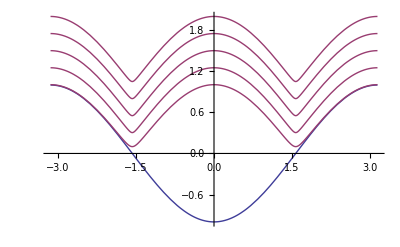

```mathematica
Plot[{ek[x],Evaluate[Table[Ep[0.1,Δ,x],{Δ,0.,1,0.25}]]},{x,-π,π}]
```

```mathematica
f=.
REL1=d^2 f^2(e-x)^2+(((e-x)^2)[f^2-(e+x)^2])^2+d^2(e-x)^2(e+x)^2+f^2(f^2-(e+x)^2)^2
REL2=d^2 f^2(e+x)^2+(((e+x)^2)[f^2-(e-x)^2])^2+d^2(e+x)^2(e-x)^2+f^2(f^2-(e-x)^2)^2
FullSimplify[REL1]
FullSimplify[REL2]
```

d^2 f^2 (e-x)^2+d^2 (e-x)^2 (e+x)^2+f^2 (f^2-(e+x)^2)^2+((e-x)^2[f^2-(e+x)^2])^2

f^2 (f^2-(e-x)^2)^2+d^2 f^2 (e+x)^2+d^2 (e-x)^2 (e+x)^2+((e+x)^2[f^2-(e-x)^2])^2

f^2 (e-f+x)^2 (e+f+x)^2+d^2 (e-x)^2 (f^2+(e+x)^2)+((e-x)^2[f^2-(e+x)^2])^2

d^2 (f^2+(e-x)^2) (e+x)^2+f^2 (e+f-x)^2 (-e+f+x)^2+((e+x)^2[(e+f-x) (-e+f+x)])^2

```mathematica
VEL1=((f^2+(e-x)^2)[f^2-(e+x)^2])^2+d^2((e-x)^2)[f^2+(e+x)^2]
VEL2=((f^2+(e+x)^2)[f^2-(e-x)^2])^2+d^2((e+x)^2)[f^2+(e-x)^2]
FullSimplify[VEL1*VEL2]
```

((f^2+(e-x)^2)[f^2-(e+x)^2])^2+d^2  (e-x)^2[f^2+(e+x)^2]

d^2  (e+x)^2[f^2+(e-x)^2]+((f^2+(e+x)^2)[f^2-(e-x)^2])^2

(((f^2+(e-x)^2)[f^2-(e+x)^2])^2+d^2  (e-x)^2[f^2+(e+x)^2]) (d^2  (e+x)^2[f^2+(e-x)^2]+((f^2+(e+x)^2)[(e+f-x) (-e+f+x)])^2)